# Интерполационен полином на Лаграж

## Стъпки за решаване: 1. Генерираме данни (съставяне на таблицата) x_i = 7 + i * (0.17), i = -7,7 y_i = f(x_i) f(x) = 3sin(x-7) x 5.81 5.98 .... y -2.785 -2.556 .... 2. f(p) ≈ ? а) p = 6.18 - интерполация б) p = 5.78 - екстраполация в) p = 30 - екстраполация |R_n(x)| <= (M_(n+1))/((n+1)!)|(x-x_0)....(x-x_n)| L_n(x) = ∑ .... ∏

## Линейна интерполация L_1(x) = ?, L_1(p) = ? (n = 1) x 6.15 6.32 y -2.2538 -1.886

## Интерполационни условия: L_n(x_i) = y_i

## L_1(x) = - 2.2538 (x - 6.32)/(6.15 - 6.32) - 1.886 (x - 6.15)/(6.32 - 6.15)

## Генериране на данни

```mathematica
xt = Table[7 + i*0.17, {i, -7,7}]
```

{5.81,5.98,6.15,6.32,6.49,6.66,6.83,7.,7.17,7.34,7.51,7.68,7.85,8.02,8.19}

```mathematica
f[x_] := 3Sin[x-7]
```

```mathematica
yt =f[xt]
```

{-2.78511,-2.55632,-2.25384,-1.88638,-1.46453,-1.00046,-0.507547,0.,0.507547,1.00046,1.46453,1.88638,2.25384,2.55632,2.78511}

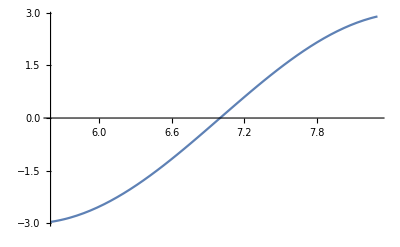

```mathematica
grf = Plot[f[x], {x, 5.6,8.3}]
```

```mathematica
n = Length[xt]
```

15

```mathematica
points = Table[{xt[[i]], yt[[i]]}, {i, 1, n}]
```

{{5.81,-2.78511},{5.98,-2.55632},{6.15,-2.25384},{6.32,-1.88638},{6.49,-1.46453},{6.66,-1.00046},{6.83,-0.507547},{7.,0.},{7.17,0.507547},{7.34,1.00046},{7.51,1.46453},{7.68,1.88638},{7.85,2.25384},{8.02,2.55632},{8.19,2.78511}}

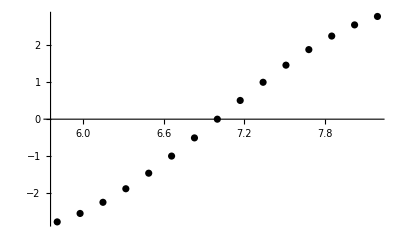

```mathematica
grp = ListPlot[points, PlotStyle->Black]
```

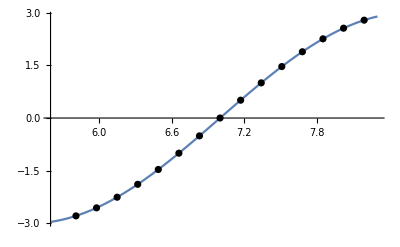

```mathematica
Show[grf, grp]
```

## Линейна интерполация

```mathematica
L1[x_] := - 2.2538 * (x - 6.32)/(6.15-6.32) -1.886 * (x - 6.15)/(6.32 - 6.15)
```

```mathematica
Expand[L1[x]]
```

-15.5595+2.16353 x

### Проверка на интерполационните условия

```mathematica
L1[6.15]
L1[6.32]
```

-2.2538

-1.886

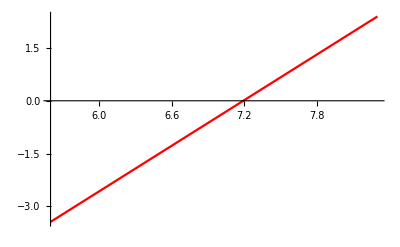

```mathematica
grL1 = Plot[L1[x], {x, 5.6, 8.3}, PlotStyle->Red]
```

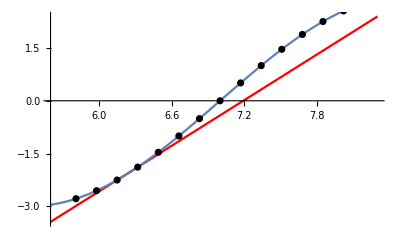

```mathematica
Show[grL1, grf, grp]
```

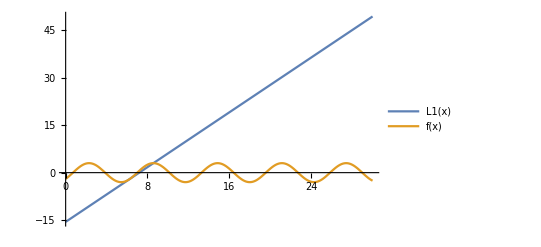

```mathematica
grL1 = Plot[{L1[x], f[x]}, {x, 0, 30},PlotLegends->"Expressions"]
```

### Пресмятане на приближена стойност

```mathematica
L1[6.18]
```

-2.18889

За сравнение с истинската стойност

```mathematica
f[6.18]
```

-2.19344

### Оценка на грешката

#### Теоретична грешка

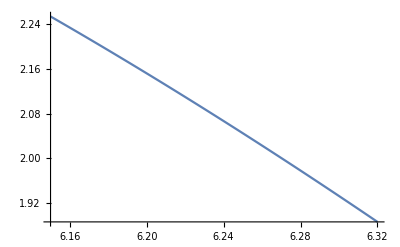

```mathematica
Plot[Abs[f''[x]], {x,6.15,6.32}]
```

```mathematica
M2 = Abs[f''[6.15]]
```

2.25384

```mathematica
R1[x_] := M2/(2!)Abs[(x-6.15)(x-6.32)]
```

```mathematica
R1[6.18]
```

0.00473307

#### Истинска грешка

```mathematica
Abs[L1 [6.18] - f[6.18]]
```

0.00454337

## Квадратична интерполация

```mathematica
L2[x_] :=-2.556 * ((x - 6.15)(x-6.32))/((5.98 - 6.15)(5.98-6.32))- 2.2538 * ((x - 5.98)(x-6.32))/((6.15 - 5.98)(6.15-6.32))-1.886 * ((x-5.98)(x-6.15))/((6.32-5.98)(6.32-6.15))
```

```mathematica
Expand[L2[x]]
```

28.5537-11.9893 x+1.13495 x^2

### Проверка на интерполационните условия

```mathematica
L2[5.98]
L2[6.15]
L2[6.32]
```

-2.556

-2.2538

-1.886

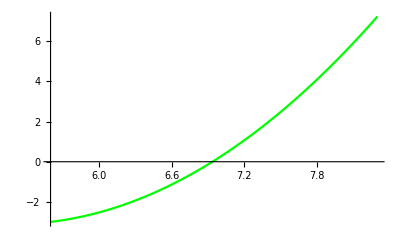

```mathematica
grL2 = Plot[L2[x], {x, 5.6, 8.3}, PlotStyle->Green]
```

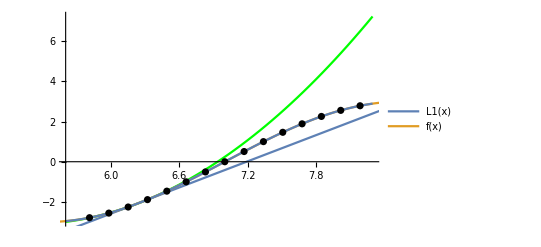

```mathematica
Show[grL2,grL1, grf, grp]
```

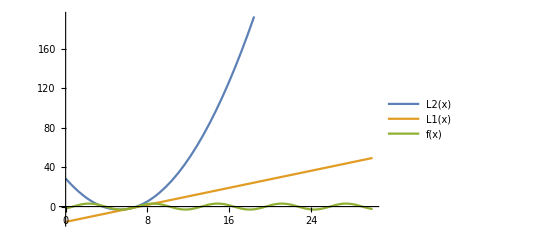

```mathematica
grL2 = Plot[{L2[x],L1[x], f[x]}, {x, 0, 30},PlotLegends->"Expressions"]
```

### Пресмятане на приближена стойност

```mathematica
L2[6.18]
```

-2.19366

За сравнение с истинската стойност

```mathematica
f[6.18]
```

-2.19344

### Оценка на грешката

#### Теоретична грешка

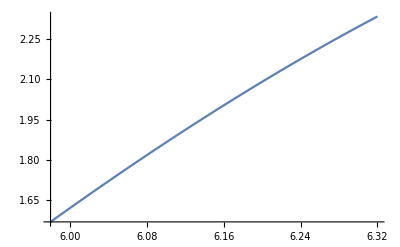

```mathematica
Plot[Abs[f'''[x]], {x,5.98,6.32}]
```

```mathematica
M3 = Abs[f'''[6.32]]
```

2.33272

```mathematica
R2[x_] := M3/(3!)Abs[(x-5.98)(x-6.15)(x-6.32)]
```

```mathematica
R2[6.18]
```

0.000326581

#### Истинска грешка

```mathematica
Abs[L2 [6.18] - f[6.18]]
```

0.00022341

## Екстраполация

```mathematica
L1[30]
```

49.3464

```mathematica
L2[30]
```

690.329

```mathematica
f[30.]
```

-2.53866

```mathematica
R1[30]
```

636.449

```mathematica
R2[30]
```

5274.17